# Trapezoidal Rule Programming Assignment

### Instructions

The purpose of this assignment is to assess your ability to code an algorithm that will perform numerical integration in Mathematica. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Question 1 (4 points)

The Trapezoidal Rule for approximating a definite integral is:

∫_a^b f(x)ⅆx≈T_n=Δx/2 [ f(x_0)+2f(x_1)+2f(x_2)+...+2f(x_(n-1))+ f(x_n)]  where Δx=(b-a)/n  and  x_i=a+iΔx.

Write the Mathematica code necessary to calculate T_n for any choice of n.  

Note that your program will be graded on both readability (in this question) and functionality (in Questions 2 and 3). Refer to the video in this assignment if you have questions.

```mathematica
trapz[f_,a_,b_,n_]:=Module[{Δx},
Δx=(b-a)/n;
Δx/2(f[a]+2Sum[f[a+Δx*i],{i,1,n-1}]+f[b])]
```

### Question 2 (2 points)

Use your code to approximate ∫_-2^5 -x^3+3ⅆx using n = 10 and n = 16 intervals.  Round your answers to 4 decimal places.  Show all your work below, but record your answers in the designated text cells.  Note that this simple integral and small choices for n provide a good opportunity to check your code!
	
∫_-2^5 -x^3+3ⅆx using n = 10 intervals

```mathematica
f[x_]=-x^3+3;
N[trapz[f,-2,5,10],7]
```

-133.8225

Approximation = -133.8225

∫_-2^5 -x^3+3ⅆx using n = 16 intervals

```mathematica
N[trapz[-2,5,16],7]
```

-132.2549

Approximation = -132.2549

### Question 3 (2 points)

Use your code to approximate ∫_-1^1 e^(4x)ⅆx using n = 200 intervals.  Round your answer to 6 decimal places.  Then use 13.64495859856388 as the actual value of  ∫_-1^1 e^(4x)ⅆx and error = actual value - approximate value  to calculate the error in your approximation.  Show all your work below, but record your answers in the designated text cells.  
	
∫_-1^1 e^(4x)ⅆx using n = 200 intervals

```mathematica
g[x_]=ⅇ^(4x);
N[trapz[g,-1,1,200],8]
```

13.646778

Approximation = 13.646778

```mathematica
13.64495859856388-trapz[g,-1,1,200]
```

-0.00181928

Error -0.00181928

### Question 4 (2 points)

In the previous question you should have gotten a negative error. Plot the function e^(4x) from x=-1 to x=1 and use that to explain why you should have expected this.

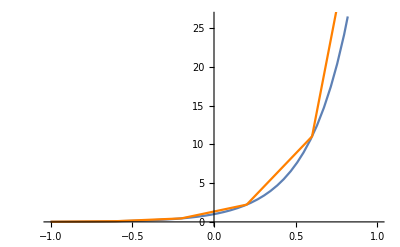

```mathematica
Show[Plot[ⅇ^(4x),{x,-1,1}],ListLinePlot[Table[{x,ⅇ^(4x)},{x,-1,1,.4}],PlotStyle->Orange]]
```

The trapezoidal approximation will produce an over estimate or negative error due to the curve having an increasing slope. The trapezoids above demonstrate an exaggerated example of what’s happening. The trapezoids are all above ⅇ^(4x) and thus produces a greater area than the integral of e^(4x) giving a negative error.